```mathematica
Table[Binomial[2*n,n]/4^n,{n,-1,10}]
```

{0,1,1/2,3/8,5/16,35/128,63/256,231/1024,429/2048,6435/32768,12155/65536,46189/262144}

```mathematica
Evaluate[{Table[#[n],{n,0,10}]}&/@{Binomial[2*#,#]/4^#&,Sqrt}]
```

{{{1,1/2,3/8,5/16,35/128,63/256,231/1024,429/2048,6435/32768,12155/65536,46189/262144}},{{0,1,√2,√3,2,√5,√6,√7,2 √2,3,√10}}}

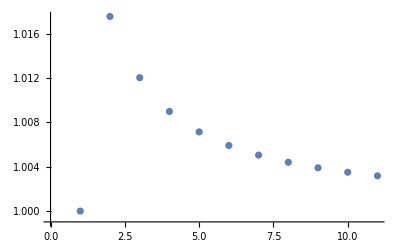

```mathematica
ListPlot[Table[#[n],{n,0,10}]&/@{Binomial[2*#,#]/4^#*Sqrt[1+Pi*#]&}]
```

```mathematica
Binomial[-4,-2]
```

0

```mathematica
Table[#[n],{n,0,10}]&/@{Binomial[2*#,#]/4^#*Sqrt[1+Pi*#]&}
```

{{1,(√(1+π))/2,3/8 √(1+2 π),5/16 √(1+3 π),35/128 √(1+4 π),63/256 √(1+5 π),(231 √(1+6 π))/1024,(429 √(1+7 π))/2048,(6435 √(1+8 π))/32768,(12155 √(1+9 π))/65536,(46189 √(1+10 π))/262144}}

```mathematica
%//N
```

{{1.,1.01755,1.01203,1.00898,1.00714,1.00592,1.00505,1.0044,1.0039,1.0035,1.00318}}